```mathematica
gr=Graph[EdgeAdd[VertexAdd[allGraphs5[lambdaKey,"graph" ],{6,7}],{1<->6,2<->6,5<->7}],VertexLabels->"Name"]
```

-Graphics-

```mathematica
EmbedGraphInGr[key_]:=Block[{val=allGraphs5[key], sets, g, sub},
sets=val["vertexsets"];
g=gr;
g=EdgeDelete[ g,{1<->2,1<->5,2<->3,3<->4,4<->5}];
Table[If[Length[s]>1,
g=VertexContract[g,s]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{First[sets[[e[[1]]]]]<->First[sets[[e[[2]]]]]}],{e,EdgeList[sub]}];

Graph[VertexList[g],DeleteDuplicates[EdgeList[g]],VertexLabels->"Name"]
]
```

## Now Some test

```mathematica
allGraphs5[lambdaKey,"children"]
```

{{27226,35977},{22852,31681},{20746,23041},{20692,20803},{20668,27259}}

```mathematica
allGraphs5[19683,"graph"]
```

-Graphics-

```mathematica
parts=Table[
Simplify[
Total[
Table[
With[{current=EmbedGraphInGr[atom]},
With[{left=VertexDelete[current,7],
right=VertexDelete[current,6]},
Simplify[(ChromaticPolynomial[left,x]*ChromaticPolynomial[right,x])/ChromaticPolynomial[allGraphs5[atom,"graph"],x]]
]
],
{atom,children}]
]
],
{children,allGraphs5[lambdaKey,"children"]}]
```

{x (2-3 x+x^2)^2 (2-2 x+x^2),x (2-3 x+x^2)^2 (2-2 x+x^2),x (2-3 x+x^2)^2 (2-2 x+x^2),x (2-3 x+x^2)^2 (2-2 x+x^2),x (2-3 x+x^2)^2 (2-2 x+x^2)}

```mathematica
parts=Table[
With[{current=EmbedGraphInGr[atom]},
With[{left=VertexDelete[current,7],
right=VertexDelete[current,6]},
Simplify[(ChromaticPolynomial[left,x]*ChromaticPolynomial[right,x])/ChromaticPolynomial[allGraphs5[atom,"graph"],x]]
]
],
{atom,{lambdaKey}}]//Factor
```

{(-2+x)^2 (-1+x)^2 x (2-2 x+x^2)}

```mathematica
ChromaticPolynomial[gr,x]//Factor
```

(-2+x)^2 (-1+x)^2 x (2-2 x+x^2)

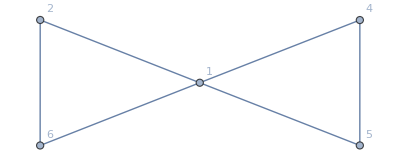
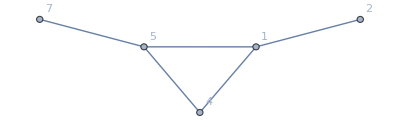
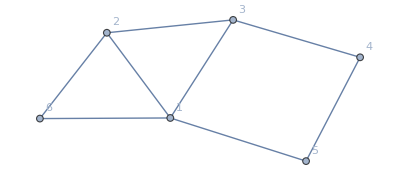
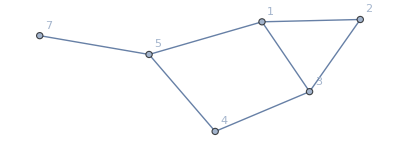
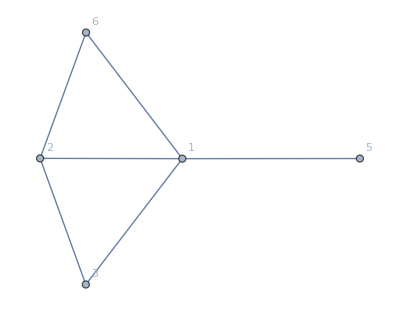
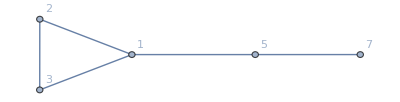
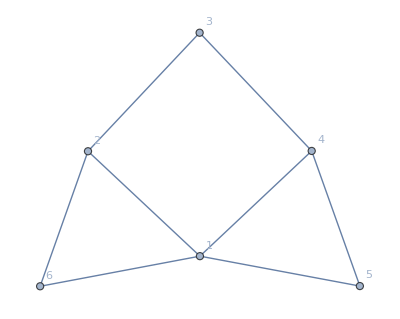
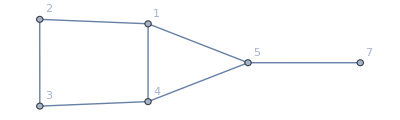
{-Graphics-→(-Graphics- -Graphics-)/(-Graphics-)+(-Graphics- -Graphics-)/(-Graphics-),-Graphics-→(-Graphics- -Graphics-)/(-Graphics-)+(-Graphics- -Graphics-)/(-Graphics-),-Graphics-→(-Graphics- -Graphics-)/(-Graphics-)+(-Graphics- -Graphics-)/(-Graphics-),-Graphics-→(-Graphics- -Graphics-)/(-Graphics-)+(-Graphics- -Graphics-)/(-Graphics-),-Graphics-→(-Graphics- -Graphics-)/(-Graphics-)+(-Graphics- -Graphics-)/(-Graphics-)}

```mathematica
Table[
gr->
Simplify[
Total[
Table[
With[{current=EmbedGraphInGr[atom]},
With[{left=VertexDelete[current,7],
right=VertexDelete[current,6]},
Simplify[(left*right)/allGraphs5[atom,"graph"]]
]
],
{atom,children}]
]
],
{children,allGraphs5[lambdaKey,"children"]}]
```

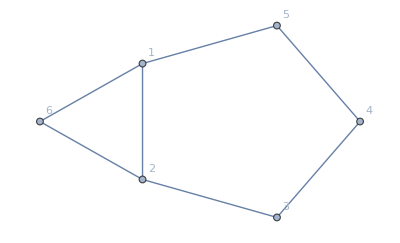
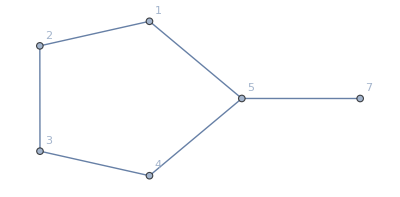
-Graphics-(-2+x)^2 (-1+x)^2 x (2-2 x+x^2)→(-Graphics-(-2+x)^2 x (-2+4 x-3 x^2+x^3) -Graphics-(-2+x) (-1+x)^2 x (2-2 x+x^2))/(-Graphics-(-2+x) (-1+x) x (2-2 x+x^2))

```mathematica
Labeled[gr,Factor[ChromaticPolynomial[gr,x]]]->
Simplify[
Total[
Table[
With[{current=EmbedGraphInGr[atom]},
With[{left=VertexDelete[current,7],
right=VertexDelete[current,6]},
Factor[(Labeled[left,Simplify[ChromaticPolynomial[left,x]]]*Labeled[right,Factor[ChromaticPolynomial[right,x]]])/
Labeled[allGraphs5[atom,"graph"],Factor[ChromaticPolynomial[allGraphs5[atom,"graph"],x]]]
]
]
],
{atom,{lambdaKey}}]
]
]
```

```mathematica
((-2+x)^2 x (-2+4 x-3 x^2+x^3))*((-2+x) (-1+x)^2 x (2-2 x+x^2))/((-2+x) (-1+x) x (2-2 x+x^2))//Factor
```

```mathematica
(-2+x)^2 (-1+x)^2 x (2-2 x+x^2)==((-2+x)^2 (-1+x)^2 x (2-2 x+x^2))
```

True